```mathematica
DSolve[{(a+b z)y''[z]+b y'[z]==0,y[-1]==1,y[1]==-1},y[z],z]
```

{{y[z]→(-Log[a-b]-Log[a+b]+2 Log[a+b z])/(Log[a-b]-Log[a+b])}}

```mathematica
D[(-Log[a-b]-Log[a+b]+2 Log[a+b z])/(Log[a-b]-Log[a+b]),z]
```

(2 b)/((a+b z) (Log[a-b]-Log[a+b]))

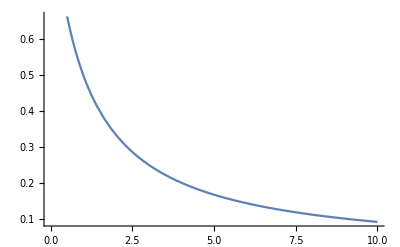

```mathematica
Plot[1/(1+z),{z,0,10}]
```

```mathematica
f[z_]:=-2γ/(1/σ-γ z)/(Log[1/σ+γ]-Log[1/σ-γ])
```

```mathematica
f[1]
```

-(2 γ)/((-γ+1/σ) (-Log[-γ+1/σ]+Log[γ+1/σ]))

```mathematica
DSolve[λ^2(-k^2y[z]+y''[z])+λ γ D[(-k^2y[z]+y''[z]),z]-(λ+(1/σ-γ z)λ)(k^4y[z]-2k^2y''[z]+y''''[z])-γ D[(k^4y[z]-2k^2y''[z]+y''''[z]),z]+(1/σ-γ z)(-k^6y[z]+3k^4y''[z]-3k^2y''''[z]+y''''''[z])==y[z]f[z]k^2 R/σ,y[z],z]
```

$Aborted

```mathematica
λ^2(-k^2y[z]+y''[z])+λ γ D[(-k^2y[z]+y''[z]),z]
```

λ^2 (-k^2 y[z]+y''[z])+γ λ (-k^2 y'[z]+y^(3)[z])

```mathematica
-(λ+(1/σ-γ z)λ)(k^4y[z]-2k^2y''[z]+y''''[z])-γ D[(k^4y[z]-2k^2y''[z]+y''''[z]),z]
```

(-λ-λ (-z γ+1/σ)) (k^4 y[z]-2 k^2 y''[z]+y^(4)[z])-γ (k^4 y'[z]-2 k^2 y^(3)[z]+y^(5)[z])

```mathematica
(1/σ-γ z)(-k^6y[z]+3k^4y''[z]-3k^2y''''[z]+y''''''[z])
```

(-z γ+1/σ) (-k^6 y[z]+3 k^4 y''[z]-3 k^2 y^(4)[z]+y^(6)[z])

```mathematica
Expand[(-a+b)^3]
```

-a^3+3 a^2 b-3 a b^2+b^3

```mathematica
Simplify[Solve[R==((κ+1)^2-4 κ (k^2+l^2)^2) (k^2+l^2)/k^2/κ,κ]]/.{k->
```

{{κ→(-2 q^2+4 q^6+k^2 R-√(-4 q^4+(-2 q^2+4 q^6+k^2 R)^2))/(2 q^2)},{κ→(-2 q^2+4 q^6+k^2 R+√(-4 q^4+(-2 q^2+4 q^6+k^2 R)^2))/(2 q^2)}}

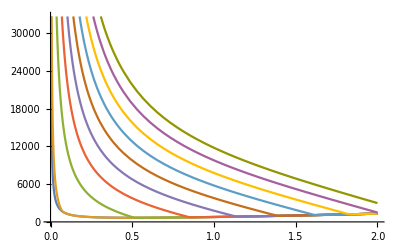

```mathematica
Plot[Evaluate@Table[Max[2(x+1)/κ /x((κ+1)^2-π^4 4κ (x+1)^2),π^4(x+1)^3/x],{κ,1,5000,500}],{x,0,2}]
```

```mathematica
NSolve[{2(x+1)/κ /x((κ+1)^2-π^4 4κ (x+1)^2)==π^4(x+1)^3/x,π^4(x+1)^3/x==R},{x,κ}][[2]]
```

{x→-1.+(0.0885122 R)/((-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+0.0386613 (-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3),κ→0.25 (872.682+1753.36 (-1.+(0.0885122 R)/((-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+0.0386613 (-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+876.682 (-1.+(0.0885122 R)/((-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+0.0386613 (-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))^2+√(-16.+(872.682+1753.36 (-1.+(0.0885122 R)/((-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+0.0386613 (-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+876.682 (-1.+(0.0885122 R)/((-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))+0.0386613 (-88.8264 R+1.73205 √(2630.05 R^2-4. R^3))^(1/3))^2)^2))}

```mathematica
kappa[R_]:=Re[0.25 (872.6818193060219+1753.3636386120438 (-1.+(0.08851220669390532 R)/((-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3))+0.03866126732924858 (-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3))+876.6818193060219 (-1.+(0.08851220669390532 R)/(-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3)+0.03866126732924858 (-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3))^2+√(-16.+(872.6818193060219+1753.3636386120438 (-1.+(0.08851220669390532 R)/(-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3)+0.03866126732924858 (-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3))+876.6818193060219 (-1.+(0.08851220669390532 R)/(-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3)+0.03866126732924858 (-88.82643960980423 R+1.7320508075688772 √(2630.0454579180655 R^2-4. R^3))^(1/3))^2)^2))]
```

```mathematica
kappa[10000]
```

40305.3

```mathematica
Needs["NumericalCalculus`"]
```

NSeries::shdw: Symbol "NSeries" appears in multiple contexts {"NumericalCalculus`", "Global`"}; definitions in context "NumericalCalculus`" may shadow or be shadowed by other definitions.

```mathematica
NSeries[kappa[x],{x,4000,1}]
```

2.07939/(x-4000)+14912.1+2.07939 (x-4000)+O[x-4000]^2

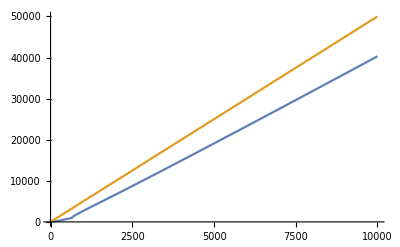

```mathematica
Plot[{kappa[x],5 x - 2},{x,000,10000}]
```

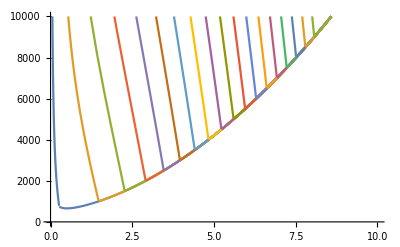

```mathematica
Plot[Evaluate@Table[Max[2(x+1)/κ /x((κ+1)^2-π^4 4κ (x+1)^2),π^4(x+1)^3/x,π^4(x+1)^3/x]/.{κ->kappa[R]},{R,500,9000,500}],{x,0,10},PlotRange->{0,10000}]
```

```mathematica
Max[2(x+1)/κ /x((κ+1)^2-π^4 4κ (x+1)^2),π^4(x+1)^3/x,π^4(x+1)^3/x]/.{κ->kappa[9000]}
```

Max[(π^4 (1+x)^3)/x,(0.0000555077 (1+x) (1.29831×10^9-1.4039×10^7 (1+x)^2))/x]

```mathematica
Simplify[π^4(x+1)^3/x/.{x->(-3 π^2 κ+√2 √(κ+2 κ^2+κ^3))/(3 π^2 κ)}]
```

-(2 √2 (κ (1+κ)^2)^(3/2))/(9 κ^2 (3 π^2 κ-√2 √(κ (1+κ)^2)))

```mathematica
Simplify[
```

```mathematica
NSolve[-(2 √2 (κ (1+κ)^2)^(3/2))/(9 κ^2 (3 π^2 κ-√2 √(κ (1+κ)^2)))==8000,κ]
```

{{κ→447.493},{κ→0.00223467},{κ→0.0000314768}}

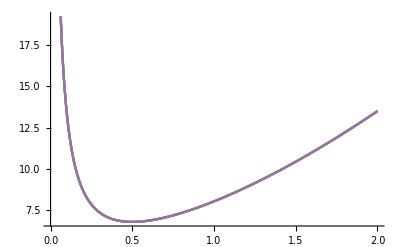

```mathematica
Plot[Evaluate@Table[(x+1)^3/x,{κ,1,5}],{x,0,2}]
```